```mathematica
fr[x_]:=Block[{c=x,i=IntegerDigits[x,2]},FromDigits[i,2]/(2^Length[i]-1)]
```

```mathematica
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr[#1]==fr[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

```mathematica
ccc={2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839};
```

```mathematica
fr3[x_]:=Block[{c=x,i=IntegerDigits[x,3]},FromDigits[i,3]/(3^Length[i]-1)]
```

```mathematica
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr3[#1]==fr3[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{3,6,10,22,25,34,43,52,61,70,110,230,239,259,265,292,319,346,373,400,427,433,453,480,507,520,533,560,587,607,613,640,667,694,1058,2150,2177,2258,2339,2420,2501,2582,2663,2744,2825,2906,2987,3068,3149,3230,3311,3392,3473,3554,3635,3716,3797,3878,3959,4040,4121,4202,4283,4364,4445,4526,4607,4688,4769,4850,4931,5012,5093,5174,5255,5336,5417,5498,5579,5660,5741,5822,5903,5984,6065,6146,6227,6308,6389,6470,6722,7478,8234,8990,9746}

```mathematica
fr4[x_]:=Block[{c=x,i=IntegerDigits[x,4]},FromDigits[i,4]/(4^Length[i]-1)]
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr4[#1]==fr4[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{4,8,12,17,37,57,61,77,93,109,125,141,157,173,189,205,221,237,322,662,1002,1018,1069,1081,1145,1209,1273,1337,1401,1465,1529,1593,1605,1656,1720,1784,1848,1873,1911,1975,2039,2103,2141,2166,2230,2294,2358,2409,2421,2485,2549,2613,2677,2741,2805,2869,2933,2945,2996,3060,3124,3188,3213,3251,3315,3379,3443,3481,3506,3570,3634,3698,3749,3761,3825,3889,3953,4017,5382}

```mathematica
fr5[x_]:=Block[{c=x,i=IntegerDigits[x,5]},FromDigits[i,5]/(5^Length[i]-1)]
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr5[#1]==fr5[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{5,10,15,20,26,56,86,116,121,146,171,196,221,246,271,296,321,346,371,396,421,446,471,496,521,546,571,596,752,1532,2312,3092,3117,3221,3241,3366,3491,3616,3741,3866,3991,4116,4241,4366,4491,4511,4615,4740,4865,4990,5115,5156,5239,5364,5489,5614,5739,5801,5863,5988,6113,6238,6363,6446,6487,6612,6737,6862,6987,7091,7111,7236,7361,7486,7611,7736,7861,7986,8111,8236,8361,8381,8485,8610,8735,8860,8985,9026,9109,9234,9359,9484,9609,9671,9733,9858}

```mathematica
fr6[x_]:=Block[{c=x,i=IntegerDigits[x,6]},FromDigits[i,6]/(6^Length[i]-1)]
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr6[#1]==fr6[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{6,12,18,24,30,37,79,121,163,205,211,247,283,319,355,391,427,463,499,535,571,607,643,679,715,751,787,823,859,895,931,967,1003,1039,1075,1111,1147,1183,1219,1255,1514,3068,4622,6176,7730,7766,7951,7981,8197,8413,8629,8845,9061,9277,9493,9709,9925}

```mathematica
fr7[x_]:=Block[{c=x,i=IntegerDigits[x,7]},FromDigits[i,7]/(7^Length[i]-1)]
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr7[#1]==fr7[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{7,14,21,28,35,42,50,106,162,218,274,330,337,386,435,484,533,582,631,680,729,778,827,876,925,974,1023,1072,1121,1170,1219,1268,1317,1366,1415,1464,1513,1562,1611,1660,1709,1758,1807,1856,1905,1954,2003,2052,2101,2150,2199,2248,2297,2346,2746,5546,8346}

```mathematica
fr8[x_]:=Block[{c=x,i=IntegerDigits[x,8]},FromDigits[i,8]/(8^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr8[#1]==fr8[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{859.041,{8,16,24,32,40,48,56,65,137,209,281,353,425,497,505,569,633,697,761,825,889,953,1017,1081,1145,1209,1273,1337,1401,1465,1529,1593,1657,1721,1785,1849,1913,1977,2041,2105,2169,2233,2297,2361,2425,2489,2553,2617,2681,2745,2809,2873,2937,3001,3065,3129,3193,3257,3321,3385,3449,3513,3577,3641,3705,3769,3833,3897,3961,4025,4610,9290}}

```mathematica
fr9[x_]:=Block[{c=x,i=IntegerDigits[x,9]},FromDigits[i,9]/(9^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr9[#1]==fr9[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{808.343,{9,18,27,36,45,54,63,72,82,172,262,352,442,532,622,712,721,802,883,964,1045,1126,1207,1288,1369,1450,1531,1612,1693,1774,1855,1936,2017,2098,2179,2260,2341,2422,2503,2584,2665,2746,2827,2908,2989,3070,3151,3232,3313,3394,3475,3556,3637,3718,3799,3880,3961,4042,4123,4204,4285,4366,4447,4528,4609,4690,4771,4852,4933,5014,5095,5176,5257,5338,5419,5500,5581,5662,5743,5824,5905,5986,6067,6148,6229,6310,6391,6472,7292}}

```mathematica
fr10[x_]:=Block[{c=x,i=IntegerDigits[x,10]},FromDigits[i,10]/(10^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr10[#1]==fr10[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{855.33,{10,20,30,40,50,60,70,80,90,101,211,321,431,541,651,761,871,981,991,1091,1191,1291,1391,1491,1591,1691,1791,1891,1991,2091,2191,2291,2391,2491,2591,2691,2791,2891,2991,3091,3191,3291,3391,3491,3591,3691,3791,3891,3991,4091,4191,4291,4391,4491,4591,4691,4791,4891,4991,5091,5191,5291,5391,5491,5591,5691,5791,5891,5991,6091,6191,6291,6391,6491,6591,6691,6791,6891,6991,7091,7191,7291,7391,7491,7591,7691,7791,7891,7991,8091,8191,8291,8391,8491,8591,8691,8791,8891,8991,9091,9191,9291,9391,9491,9591,9691,9791,9891}}

```mathematica
fr11[x_]:=Block[{c=x,i=IntegerDigits[x,11]},FromDigits[i,11]/(11^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr11[#1]==fr11[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{882.481,{11,22,33,44,55,66,77,88,99,110,122,254,386,518,650,782,914,1046,1178,1310,1321,1442,1563,1684,1805,1926,2047,2168,2289,2410,2531,2652,2773,2894,3015,3136,3257,3378,3499,3620,3741,3862,3983,4104,4225,4346,4467,4588,4709,4830,4951,5072,5193,5314,5435,5556,5677,5798,5919,6040,6161,6282,6403,6524,6645,6766,6887,7008,7129,7250,7371,7492,7613,7734,7855,7976,8097,8218,8339,8460,8581,8702,8823,8944,9065,9186,9307,9428,9549,9670,9791}}

```mathematica
fr12[x_]:=Block[{c=x,i=IntegerDigits[x,12]},FromDigits[i,12]/(12^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr12[#1]==fr12[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{856.151,{12,24,36,48,60,72,84,96,108,120,132,145,301,457,613,769,925,1081,1237,1393,1549,1705,1717,1861,2005,2149,2293,2437,2581,2725,2869,3013,3157,3301,3445,3589,3733,3877,4021,4165,4309,4453,4597,4741,4885,5029,5173,5317,5461,5605,5749,5893,6037,6181,6325,6469,6613,6757,6901,7045,7189,7333,7477,7621,7765,7909,8053,8197,8341,8485,8629,8773,8917,9061,9205,9349,9493,9637,9781}}

```mathematica
fr13[x_]:=Block[{c=x,i=IntegerDigits[x,13]},FromDigits[i,13]/(13^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr13[#1]==fr13[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{834.048,{13,26,39,52,65,78,91,104,117,130,143,156,170,352,534,716,898,1080,1262,1444,1626,1808,1990,2172,2185,2354,2523,2692,2861,3030,3199,3368,3537,3706,3875,4044,4213,4382,4551,4720,4889,5058,5227,5396,5565,5734,5903,6072,6241,6410,6579,6748,6917,7086,7255,7424,7593,7762,7931,8100,8269,8438,8607,8776,8945,9114,9283,9452,9621,9790}}

```mathematica
fr14[x_]:=Block[{c=x,i=IntegerDigits[x,14]},FromDigits[i,14]/(14^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr14[#1]==fr14[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{825.411,{14,28,42,56,70,84,98,112,126,140,154,168,182,197,407,617,827,1037,1247,1457,1667,1877,2087,2297,2507,2717,2731,2927,3123,3319,3515,3711,3907,4103,4299,4495,4691,4887,5083,5279,5475,5671,5867,6063,6259,6455,6651,6847,7043,7239,7435,7631,7827,8023,8219,8415,8611,8807,9003,9199,9395,9591,9787}}

```mathematica
fr15[x_]:=Block[{c=x,i=IntegerDigits[x,15]},FromDigits[i,15]/(15^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr15[#1]==fr15[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

$Aborted

```mathematica
fr16[x_]:=Block[{c=x,i=IntegerDigits[x,16]},FromDigits[i,16]/(16^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr16[#1]==fr16[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{872.026,{16,32,48,64,80,96,112,128,144,160,176,192,208,224,240,257,529,801,1073,1345,1617,1889,2161,2433,2705,2977,3249,3521,3793,4065,4081,4337,4593,4849,5105,5361,5617,5873,6129,6385,6641,6897,7153,7409,7665,7921,8177,8433,8689,8945,9201,9457,9713}}

```mathematica
fr17[x_]:=Block[{c=x,i=IntegerDigits[x,17]},FromDigits[i,17]/(17^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[10000],fr17[#1]==fr17[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

{822.44,{17,34,51,68,85,102,119,136,153,170,187,204,221,238,255,272,290,596,902,1208,1514,1820,2126,2432,2738,3044,3350,3656,3962,4268,4574,4880,4897,5186,5475,5764,6053,6342,6631,6920,7209,7498,7787,8076,8365,8654,8943,9232,9521,9810}}

```mathematica
fr[x_]:=Block[{c=x,i=IntegerDigits[x,2]},FromDigits[i,2]/(2^Length[i]-1)]
Timing[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=DeleteDuplicates[Range[100],fr[#1]==fr[#2]&]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]]
```

```mathematica
frr[{list_,x_},y_]:=NestWhile[{Piecewise[{{Append[#[[1]],#[[2]]], Position[Block[{f=fr[#[[2]]]},Map[fr[#]==f&,#[[1]]]],True]=={}}, {#[[1]], True}}],#[[2]]+1}&,{list,x},1,y-1]
```

```mathematica
frr[{{},1},10000]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,«9705»,9899,9900,9901,9902,9903,9904,9905,9906,9907,9908,9909,9910,9911,9912,9913,9914,9915,9916,9917,9918,9919,9920,9921,9922,9923,9924,9925,9926,9927,9928,9929,9930,9931,9932,9934,9935,9936,9937,9938,9939,9940,9941,9942,9943,9944,9945,9946,9947,9948,9949,9950,9951,9952,9953,9954,9955,9956,9957,9958,9959,9960,9961,9962,9963,9964,9965,9966,9967,9968,9969,9970,9971,9972,9973,9974,9975,9976,9977,9978,9979,9980,9981,9982,9983,9984,9985,9986,9987,9988,9989,9990,9991,9992,9993,9994,9995,9996,9997,9998},9999}

```mathematica
frr[{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99},100},100]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,128,129,130,131,132,133,134,135,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,188,189,190,191,192,193,194,195,196,197},198}

```mathematica
{Block[{d=%[[1]]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]],%[[2]]}
```

{{1,2,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1},198}

```mathematica
frs[{list_,x_},y_]:=Piecewise[{{NestWhile[{Piecewise[{{Append[#[[1]],#[[2]]], Position[Block[{f=fr[#[[2]]]},Map[fr[#]==f&,#[[1]]]],True]=={}}, {#[[1]], True}}],#[[2]]+1}&,{list,x},Abs[#[[1]][[-1]]-#[[1]][[-2]]]==1&,1,y-1], Abs[list[[-1]]-list[[-2]]]==1}, {NestWhile[{Piecewise[{{Append[#[[1]],#[[2]]], Position[Block[{f=fr[#[[2]]]},Map[fr[#]==f&,#[[1]]]],True]=={}}, {#[[1]], True}}],#[[2]]+1}&,{Piecewise[{{Append[list,{list,x}[[2]]], Position[Block[{f=fr[{list,x}[[2]]]},Map[fr[#]==f&,{list,x}[[1]]]],True]=={}}, {list[[1]], True}}],{list,x}[[2]]+1},Abs[#[[1]][[-1]]-#[[1]][[-2]]]==1&,1,y-1], True}}]
```

```mathematica
frs[{{1,2,4,5,6,8},9},100]
```

{{1,2,4,5,6,8,9,11},12}

```mathematica
frs[{{1,2,4,5,6,8,9,11},12},100]
```

{{1,2,4,5,6,8,9,11,12,13,14,16},17}

```mathematica
frs[%,100]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32},33}

```mathematica
frs[%,100]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37},38}

```mathematica
frs[{{1,2,4,5,6,8,9},9},100]
```

{{1,2,4,5,6,8,9,11},12}

```mathematica
Position[Block[{f=fr[3]},Map[fr[#]==f&,{2}]],True]=={}
```

True

```mathematica
Block[{d=ccc},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]
```

{3,2,4,15,4,5,2,8,8,63,8,16,16,16,16,16,16,16,36,72,72,72,16,32,32,32,32,21,10,32,32,32,32,32,32,32,32,32,32,1023,32,64,38,25,64,64,64,51,12,64,64,64,64,64,64,64,64,12,51,64,64,64,25,38,64,64,64,38,25,64,64,64,51,12,64,64,64,64,4095,64,128,128,128,128,128,128,128,128,128,128,128,128,128}

```mathematica
Map[fr,{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37}]
```

{1,2/3,4/7,5/7,6/7,8/15,3/5,11/15,4/5,13/15,14/15,16/31,17/31,18/31,19/31,20/31,21/31,22/31,23/31,24/31,25/31,26/31,27/31,28/31,29/31,30/31,32/63,11/21,34/63,5/9,37/63}

```mathematica
frs[{{2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839},10000},100]
```

{{2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839,10000},10001}

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[%,200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[%,200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,«47345»,47658,47659,47660,47661,47662,47663,47664,47665,47666,47667,47668,47669,47670,47671,47672,47673,47674,47675,47676,47677,47678,47679,47680,47681,47682,47683,47684,47685,47686,47687,47688,47689,47690,47691,47692,47693,47694,47695,47696,47697,47698,47699,47700,47701,47702,47703,47704,47705,47706,47707,47708,47709,47710,47711,47712,47713,47714,47715,47716,47717,47718,47719,47720,47721,47722,47723,47724,47725,47726,47727,47728,47729,47730,47731,47732,47733,47734,47735,47736,47737,47738,47739,47740,47741,47742,47743,47744,47745,47746},47747}

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,«48113»,48429,48430,48431,48432,48433,48434,48435,48436,48437,48438,48439,48440,48441,48442,48443,48444,48445,48446,48447,48448,48449,48450,48451,48452,48453,48454,48455,48456,48457,48458,48459,48460,48461,48462,48463,48464,48465,48466,48467,48468,48469,48470,48471,48472,48473,48474,48475,48476,48477,48478,48479,48480,48481,48482,48483,48484,48485,48486,48487,48488,48489,48490,48491,48492,48493,48494,48495,48496,48497,48498,48499,48500,48501,48502,48503,48504,48505,48506,48507,48508,48509,48510,48511,48512,48513,48514,48515,48516,48517},48518}

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,«48881»,49200,49201,49202,49203,49204,49205,49206,49207,49208,49209,49210,49211,49212,49213,49214,49215,49216,49217,49218,49219,49220,49221,49222,49223,49224,49225,49226,49227,49228,49229,49230,49231,49232,49233,49234,49235,49236,49237,49238,49239,49240,49241,49242,49243,49244,49245,49246,49247,49248,49249,49250,49251,49252,49253,49254,49255,49256,49257,49258,49259,49260,49261,49262,49263,49264,49265,49266,49267,49268,49269,49270,49271,49272,49273,49274,49275,49276,49277,49278,49279,49280,49281,49282,49283,49284,49285,49286,49287,49288},49289}

```mathematica
frs[frs[frs[frs[frs[frs[%,200],200],200],200],200],200]
```

```mathematica
cdc={{}, {{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,«49649»,49971,49972,49973,49974,49975,49976,49977,49978,49979,49980,49981,49982,49983,49984,49985,49986,49987,49988,49989,49990,49991,49992,49993,49994,49995,49996,49997,49998,49999,50000,50001,50002,50003,50004,50005,50006,50007,50008,50009,50010,50011,50012,50013,50014,50015,50016,50017,50018,50019,50020,50021,50022,50023,50024,50025,50026,50027,50028,50029,50030,50031,50032,50033,50034,50035,50036,50037,50038,50039,50040,50041,50042,50043,50044,50045,50046,50047,50048,50049,50050,50051,50052,50053,50054,50055,50056,50057,50058,50059},50060}}, {}}
```

{{1,2,4,5,6,8,9,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,46,47,48,49,50,51,52,53,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,«49649»,49971,49972,49973,49974,49975,49976,49977,49978,49979,49980,49981,49982,49983,49984,49985,49986,49987,49988,49989,49990,49991,49992,49993,49994,49995,49996,49997,49998,49999,50000,50001,50002,50003,50004,50005,50006,50007,50008,50009,50010,50011,50012,50013,50014,50015,50016,50017,50018,50019,50020,50021,50022,50023,50024,50025,50026,50027,50028,50029,50030,50031,50032,50033,50034,50035,50036,50037,50038,50039,50040,50041,50042,50043,50044,50045,50046,50047,50048,50049,50050,50051,50052,50053,50054,50055,50056,50057,50058,50059},50060}

```mathematica
Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=cdc[[1]]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}]
```

{2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839,9967,10095,10223,10351,10479,10607,10735,10820,10862,10990,11118,11246,11374,11502,11630,11758,11886,12014,12142,12270,12398,12526,12654,12782,12910,13038,13166,13294,13422,13550,13678,13806,13934,14062,14190,14318,14446,14574,14702,14830,14958,15086,15214,15342,15470,15598,15726,15854,15982,16110,16238,16766,17822,18576,18877,19933,20989,22045,23101,23251,24156,25212,26268,27324,27927,28379,29435,30491,31547,32603,32731,32987,33243,33499,33755,34011,34267,34523,34779,35035,35291,35547,35803,36059,36315,36571,36827,37083,37339,37595,37851,38107,38363,38619,38875,39131,39387,39643,39899,40155,40411,40667,40923,41179,41435,41691,41947,42203,42459,42715,42971,43227,43483,43739,43995,44251,44507,44763,45019,45275,45531,45787,46043,46299,46555,46811,47067,47323,47579,47835,48091,48347,48603,48859,49115,49371,49627}

```mathematica
Block[{d=%},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]
```

{3,2,4,15,4,5,2,8,8,63,8,16,16,16,16,16,16,16,36,72,72,72,16,32,32,32,32,21,10,32,32,32,32,32,32,32,32,32,32,1023,32,64,38,25,64,64,64,51,12,64,64,64,64,64,64,64,64,12,51,64,64,64,25,38,64,64,64,38,25,64,64,64,51,12,64,64,64,64,4095,64,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,85,42,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,528,1056,754,301,1056,1056,1056,1056,150,905,1056,1056,1056,603,452,1056,1056,1056,1056,128,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256}

```mathematica
hlf[x_]:=NestWhile[#/2&,x,EvenQ]
```

```mathematica
hlf[256]
```

1

```mathematica
Table[Monitor[Flatten[Position[Map[Piecewise[{{0, #≠2}, {1, #==2}}]&,Block[{d=cdc[[1]]},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]],1]],{j,c,i}][[i]],{i,1+Flatten[Position[Map[Piecewise[{{0, hlf[#]==1}, {1, True}}]&,{3,2,4,15,4,5,2,8,8,63,8,16,16,16,16,16,16,16,36,72,72,72,16,32,32,32,32,21,10,32,32,32,32,32,32,32,32,32,32,1023,32,64,38,25,64,64,64,51,12,64,64,64,64,64,64,64,64,12,51,64,64,64,25,38,64,64,64,38,25,64,64,64,51,12,64,64,64,64,4095,64,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,85,42,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,528,1056,754,301,1056,1056,1056,1056,150,905,1056,1056,1056,603,452,1056,1056,1056,1056,128,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256}],1]]}]
```

{5,26,35,116,272,344,416,488,653,663,2006,2140,2165,2408,2420,2944,2995,3212,3250,3480,3505,3748,3760,8111,10820,10862,16766,17822,18576,18877,19933,20989,22045,23101,23251,24156,25212,26268,27324,27927,28379,29435,30491,31547,32603}

```mathematica
Block[{d=%},Table[d[[j+1]]-d[[j]],{j,1,Length[d]-1}]]
```

{-1,2,11,-11,1,-3,6,0,55,-55,8,0,0,0,0,0,0,20,36,0,0,-56,16,0,0,0,-11,-11,22,0,0,0,0,0,0,0,0,0,991,-991,32,-26,-13,39,0,0,-13,-39,52,0,0,0,0,0,0,0,-52,39,13,0,0,-39,13,26,0,0,-26,-13,39,0,0,-13,-39,52,0,0,0,4031,-4031,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-43,-43,86,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,400,528,-302,-453,755,0,0,0,-906,755,151,0,0,-453,-151,604,0,0,0,-928,128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Map[fr,{2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839,9967,10095,10223,10351,10479,10607,10735,10820,10862,10990,11118,11246,11374,11502,11630,11758,11886,12014,12142,12270,12398,12526,12654,12782,12910,13038,13166,13294,13422,13550,13678,13806,13934,14062,14190,14318,14446,14574,14702,14830,14958,15086,15214,15342,15470,15598,15726,15854,15982,16110,16238,16766,17822,18576,18877,19933,20989,22045,23101,23251,24156,25212,26268,27324,27927,28379,29435,30491,31547,32603,32731,32987,33243,33499,33755,34011,34267,34523,34779,35035,35291,35547,35803,36059,36315,36571,36827,37083,37339,37595,37851,38107,38363,38619,38875,39131,39387,39643,39899,40155,40411,40667,40923,41179,41435,41691,41947,42203,42459,42715,42971,43227,43483,43739,43995,44251,44507,44763,45019,45275,45531,45787,46043,46299,46555,46811,47067,47323,47579,47835,48091,48347,48603,48859,49115,49371,49627}]
```

{2/3,5/7,1,11/15,26/31,30/31,5/9,37/63,5/7,53/63,116/127,124/127,28/51,52/85,172/255,188/255,4/5,44/51,236/255,272/511,344/511,416/511,488/511,72/73,536/1023,568/1023,200/341,632/1023,653/1023,221/341,695/1023,727/1023,23/31,791/1023,823/1023,285/341,887/1023,919/1023,317/341,983/1023,2006/2047,2038/2047,2102/4095,428/819,433/819,743/1365,2293/4095,2357/4095,344/585,484/819,276/455,28/45,2612/4095,892/1365,548/819,2804/4095,956/1365,2932/4095,2944/4095,599/819,437/585,347/455,3187/4095,3212/4095,50/63,3314/4095,1126/1365,3442/4095,232/273,701/819,3569/4095,173/195,3697/4095,3748/4095,752/819,3824/4095,432/455,304/315,4016/4095,8111/8191,8175/8191,8303/16383,8431/16383,2853/5461,8687/16383,205/381,2981/5461,9071/16383,9199/16383,3109/5461,9455/16383,9583/16383,3237/5461,9839/16383,9967/16383,3365/5461,10223/16383,10351/16383,3493/5461,10607/16383,10735/16383,10820/16383,10862/16383,10990/16383,3706/5461,11246/16383,11374/16383,3834/5461,11630/16383,11758/16383,3962/5461,12014/16383,12142/16383,4090/5461,12398/16383,12526/16383,4218/5461,12782/16383,12910/16383,4346/5461,13166/16383,13294/16383,4474/5461,13550/16383,13678/16383,4602/5461,13934/16383,14062/16383,110/127,14318/16383,14446/16383,4858/5461,14702/16383,14830/16383,4986/5461,15086/16383,15214/16383,5114/5461,15470/16383,15598/16383,5242/5461,15854/16383,15982/16383,5370/5461,16238/16383,16766/32767,2546/4681,18576/32767,18877/32767,643/1057,139/217,22045/32767,23101/32767,23251/32767,24156/32767,25212/32767,26268/32767,27324/32767,27927/32767,28379/32767,4205/4681,30491/32767,31547/32767,32603/32767,32731/32767,32987/65535,11081/21845,33499/65535,6751/13107,11337/21845,34267/65535,34523/65535,11593/21845,7007/13107,35291/65535,697/1285,35803/65535,36059/65535,2421/4369,36571/65535,36827/65535,12361/21845,37339/65535,7519/13107,12617/21845,38107/65535,38363/65535,12873/21845,7775/13107,39131/65535,13129/21845,39643/65535,2347/3855,2677/4369,40411/65535,40667/65535,13641/21845,41179/65535,8287/13107,13897/21845,41947/65535,42203/65535,14153/21845,8543/13107,42971/65535,14409/21845,43483/65535,43739/65535,2933/4369,2603/3855,44507/65535,14921/21845,45019/65535,9055/13107,15177/21845,45787/65535,46043/65535,15433/21845,9311/13107,46811/65535,15689/21845,47323/65535,47579/65535,3189/4369,48091/65535,48347/65535,953/1285,48859/65535,9823/13107,16457/21845,49627/65535}

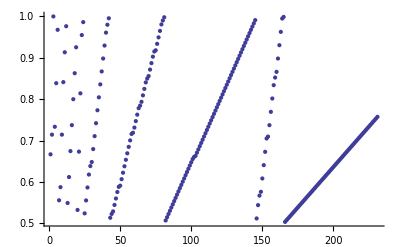

```mathematica
ListPlot[%]
```

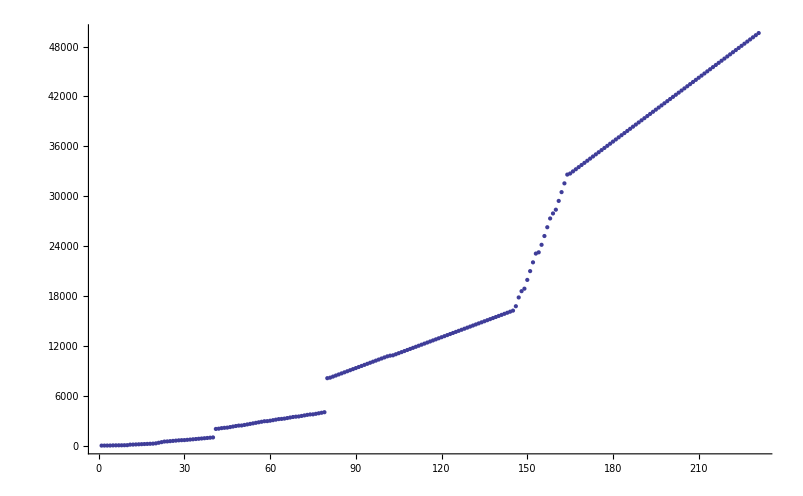

```mathematica
ListPlot[{2,5,7,11,26,30,35,37,45,53,116,124,140,156,172,188,204,220,236,272,344,416,488,504,536,568,600,632,653,663,695,727,759,791,823,855,887,919,951,983,2006,2038,2102,2140,2165,2229,2293,2357,2408,2420,2484,2548,2612,2676,2740,2804,2868,2932,2944,2995,3059,3123,3187,3212,3250,3314,3378,3442,3480,3505,3569,3633,3697,3748,3760,3824,3888,3952,4016,8111,8175,8303,8431,8559,8687,8815,8943,9071,9199,9327,9455,9583,9711,9839,9967,10095,10223,10351,10479,10607,10735,10820,10862,10990,11118,11246,11374,11502,11630,11758,11886,12014,12142,12270,12398,12526,12654,12782,12910,13038,13166,13294,13422,13550,13678,13806,13934,14062,14190,14318,14446,14574,14702,14830,14958,15086,15214,15342,15470,15598,15726,15854,15982,16110,16238,16766,17822,18576,18877,19933,20989,22045,23101,23251,24156,25212,26268,27324,27927,28379,29435,30491,31547,32603,32731,32987,33243,33499,33755,34011,34267,34523,34779,35035,35291,35547,35803,36059,36315,36571,36827,37083,37339,37595,37851,38107,38363,38619,38875,39131,39387,39643,39899,40155,40411,40667,40923,41179,41435,41691,41947,42203,42459,42715,42971,43227,43483,43739,43995,44251,44507,44763,45019,45275,45531,45787,46043,46299,46555,46811,47067,47323,47579,47835,48091,48347,48603,48859,49115,49371,49627}]
```